```mathematica
(*Código utilizado para obtener las secciones de Poincaré del sistema dada una energía y un k. Basado en el código fuente de Mathematica https://www.wolfram.com/mathematica/new-in-9/advanced-hybrid-and-differential-algebraic-equations/poincare-sections.html. Adaptado al problema por Gustavo Ardila y Cristian Tibambre*)
(*lo hacemos con k=100*)
(*Constantes y parametro de control*)
```

```mathematica
k0=100;
m=5;
g=9.8;
```

```mathematica
(*Ecuaciones diferenciales*)
ecuaciones={p'[s]==-k0*(Sin[h[s]]-Sin[j[s]])*Cos[h[s]]-m*g*Sin[h[s]], h'[s]==p[s]/m, q'[s]==k0*(Sin[h[s]]-Sin[j[s]])*Cos[j[s]]-m*g*Sin[j[s]], j'[s]==q[s]/m};
```

```mathematica
(*Guarda la sección dada la solucion obtenida usando NDSolve y si esta cumple ciertas condiciones. Aqui se usa E*)
(*poinca[{h0_,j0_,p0_,q0_}]:=Reap[NDSolve[{ecuas, h[0]==h0, j[0]==j0, p[0]==p0, q[0]==q0 , WhenEvent[j[t]==0&& q[t]≠0, Sow[{h[t],p[t]}]]},{h[t], j[t], p[t],q[t]},{t,0,1000}, MaxSteps->Infinity]][[-1,1]];*)
secciones[{a0_,b0_,c0_,d0_}]:=Reap[NDSolve[{ecuaciones, h[0]==a0, j[0]==b0, p[0]==c0, q[0]==d0, WhenEvent[q[s]==0, Sow[{h[s],p[s]}]]},{h[s],j[s], p[s], q[s]},{s,0,1000}, MaxSteps->Infinity]][[-1,1]];
```

```mathematica
info= Map[secciones, bunch]
```

{{{3.00147,25.5296},{12.2855,44.8046},{19.9718,3.41495},719,{260.213,25.1426},{267.595,23.8057},{270.65,-34.0702}},{{1},778},181,{1}}
 |  |  |  |

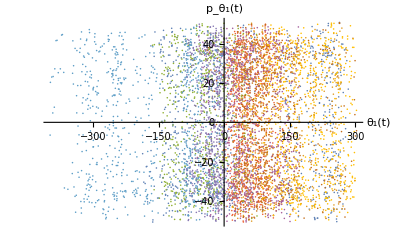

```mathematica
ListPlot[{info[[1]],info[[2]],info[[3]],info[[4]],info[[5]],info[[6]],info[[7]],info[[8]],info[[9]]}, ImageSize->Full, AxesLabel->{Style["θ_1(t)", Bold,20,Black], Style["p_θ_1(t)", Bold,20,Black]}]
```

```mathematica
Length[info]
```

261